```mathematica
(* Комплексные числа. *)
```

```mathematica
z1=a+I b
```

a+ⅈ b

```mathematica
z2 = -2+3 I
```

-2+3 ⅈ

```mathematica
Abs[z1]
```

Abs[a+ⅈ b]

```mathematica
Abs[z2]
```

√13

```mathematica
(* Вопрос: почему странный ответ для z1? *)
```

```mathematica
Conjugate[z1]
```

Conjugate[a]-ⅈ Conjugate[b]

```mathematica
Conjugate[z2]
```

-2-3 ⅈ

```mathematica
Simplify[Conjugate[z1],a∈Reals&&b∈Reals]
```

a-ⅈ b

```mathematica
Simplify[Sqrt[Conjugate[z1] z1],a∈Reals&&b∈Reals]
```

√(a^2+b^2)

```mathematica
(* Теперь мы получили ожидаемое выражение... *)
```

```mathematica
f1[t_]:=Exp[I t];
f2[t_]:=Exp[2 I t];
f3[t_]:=Exp[3 I t];
```

```mathematica
g1[t_]:=Exp[I t];
g2[t_]:=Exp[I t/2];
g3[t_]:=Exp[I t/3];
```

```mathematica
h1[t_]:=Exp[I t];
h2[t_]:=Exp[2 I t/3];
h3[t_]:=Exp[3/4 I t];
```

```mathematica
F[t_]:=f1[t]+f2[t]+f3[t];
G[t_]:=g1[t]+g2[t]+g3[t];
H[t_]:=h1[t]+h2[t]+h3[t];
```

```mathematica
Plot[F[t],{t,0,2 Pi}]
```

-Graphics-

```mathematica
(* Ничего не построилось, т.к. F[t] --- комплекснозначная функуция... *)
```

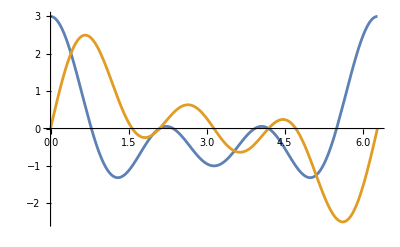

```mathematica
Plot[{Re[F[t]],Im[F[t]]},{t,0,2 Pi}]
```

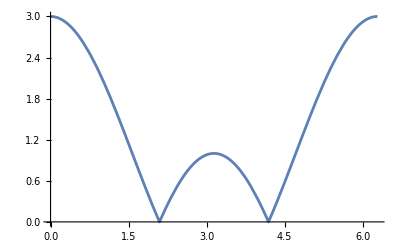

```mathematica
Plot[Abs[F[t]],{t,0,2 Pi}]
```

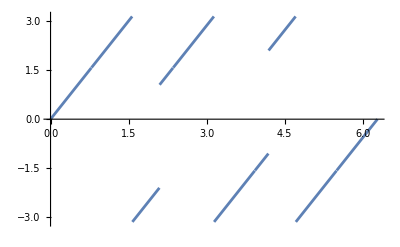

```mathematica
Plot[Arg[F[t]],{t,0,2 Pi}]
```

```mathematica
(* Вопросы: почему есть "бамп" (холмик) на графике модуля?

Можно ли как это "обойти"? 

Почему график аргумента "разрывной"? *)
```

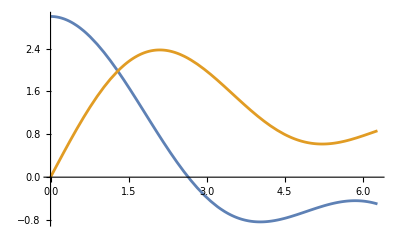

```mathematica
Plot[{Re[G[t]],Im[G[t]]},{t,0,2 Pi}]
```

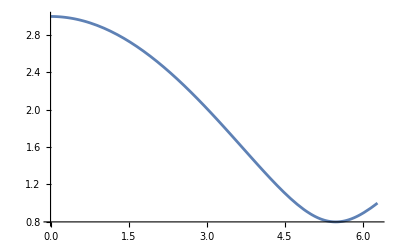

```mathematica
Plot[Abs[G[t]],{t,0,2 Pi}]
```

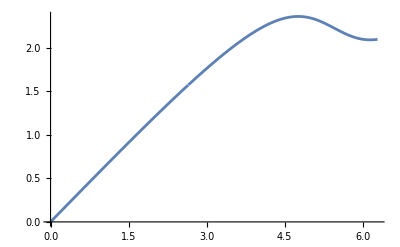

```mathematica
Plot[Arg[G[t]],{t,0,2 Pi}]
```

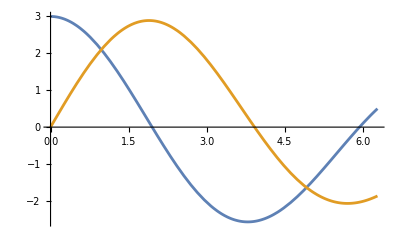

```mathematica
Plot[{Re[H[t]],Im[H[t]]},{t,0,2 Pi}]
```

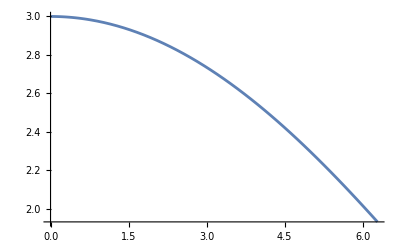

```mathematica
Plot[Abs[H[t]],{t,0,2 Pi}]
```

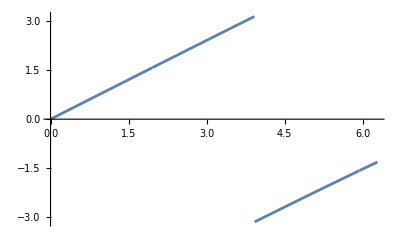

```mathematica
Plot[Arg[H[t]],{t,0,2 Pi}]
```